```mathematica
l= 10;
nx=30; 
a= 1;
fac=2.0;
dt = 2/30;
k=dt;
nsteps=300;
valImpost =1;
h=l/nx;
mw[sw_] = (sw)^fac;
mo[sw_] = (1-sw)^fac;
f[sw_]=mw[sw]/(mw[sw]+mo[sw]);
```

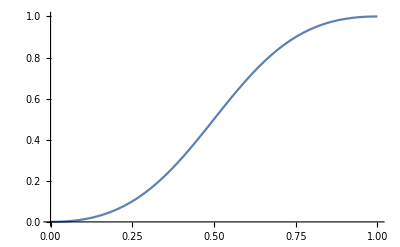

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
un= Table[0.0,{i,1, nx,1}]
dt/h


AllSolsB={};
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

1/5

```mathematica
AllSols={};
For[i=1, i<= nsteps, i++,
unphjh = Table[(0.5*(un[[j]]+un[[j+1]]))- (k/(2h))*(f[un[[j+1]]]-f[un[[j]]]),{j,1,nx-1,1}];
AppendTo[unphjh,(0.5*(k/h)(un[[-1]]+un[[-2]]))];
(*AppendTo[unphjh,0];*)



unpmhjmh = Table[0.5*(un[[j]]+un[[j-1]])-(k/(2h))*(f[un[[j]]]-f[un[[j-1]]]),{j,2,nx,1}];(*WARNING*)

PrependTo[unpmhjmh,0.5*(un[[1]]+valImpost)-(k/(2h))*(f[un[[1]]]-f[valImpost])];(*WARNING*)

(*PrependTo[unpmhjmh,0.5];*)

valfake=un[[1]]-(k/h)*(un[[1]]-valImpost);
unjp1=Table[un[[j]]-((k/h)*(f[unphjh[[j]]]-f[unpmhjmh[[j]]])),{j,2,nx-1,1}];
PrependTo[unjp1,valfake];
AppendTo[unjp1,un[[nx]]-(k/h)*(un[[nx]]-un[[nx-1]])];
unjp1=unjp1//Chop;
AppendTo[AllSols,unjp1];
un=unjp1;
];
(*

unp1B=Table[unB[[j]]-((k/h)*unB[[j]]*(unB[[j]]-unB[[j-1]])),{j,2,nx}];
PrependTo[unp1B,unB[[1]]-((k/h)*unB[[1]]*(unB[[1]]-valImpost))];
AppendTo[AllSolsB,unp1B];
unB=unp1B;*)
```

```mathematica
Manipulate[ListPlot[AllSols[[w]],Joined->True, PlotRange->{{1,nx},{0,2}}],{w,1,nsteps,1}]
```

Part::partd: Part specification AllSols[[4]] is longer than depth of object.

General::prng: Value of option PlotRange -> {{1, nx}, {0, 2}}
     is not All, Full, Automatic, a positive machine number, or an appropriate
     list of range specifications.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression Annotation[4, Charting`Private`Tag#2]
     cannot be used as a part specification.

General::stop: Further output of Part::pkspec1
     will be suppressed during this calculation.

ListPlot::lpn: Annotation[AllSols, Charting`Private`Tag#1][[Annotation[4, 
      Charting`Private`Tag#2]]] is not a list of numbers or pairs of numbers.